## Razporeditev sredstev

Podjetje ima tri oddelke, ki poslujejo z: 30% dobičkom, 20% dobičkom in brez dobička. Med oddelke želimo razporediti 40.000 evrov sredstev, pri čemer mora 1. oddelek prejeti vsaj 8.000 evrov, 2. oddelek vsaj 10.000 evrov in 3. oddelek največ dvakrat toliko kot 2. oddelek. Kako naj razporedimo sredstva, da bomo dobili čimveč dobička?

```mathematica
Maximize[{0.3x1+0.2x2,x1≥8000,x2≥ 10000,-2x2+x3≤ 0,x1+x2+x3≤ 40000,x1≥0,x2≥0,x3≥ 0},{x1,x2,x3}]
```

{11000.,{x1→30000.,x2→10000.,x3→0.}}

### Rešitev

```mathematica
Maximize[{0.3x+0.2y,x≥8,y≥10,z≤2y,x≥0,y≥0,z≥0,x+y+z≤40},{x,y,z}]
```

## Grafično reševanje

Grafično in z uporabo ukaza Minimize rešite linearni problem, podan z:

x+2y≥1
2x+y≥1
2x-y≤1

min x+y

```mathematica
Minimize[{x+y,x+2y≥1,2x+y≥1,2x-y≤1},{x,y}]
```

{2/3,{x→1/3,y→1/3}}

### Rešitev

```mathematica
Manipulate[
Show[
RegionPlot[x+2y≥1&&2x+y≥1&&2x-y≤1,{x,0,1},{y,0,1}],
ContourPlot[{x+2y==1,2x+y==1,2x-y==1,x+y==k},{x,0,1},{y,0,1}]
],{k,-3,3,0.01}]
```

```mathematica
Minimize[{x+y,x+2y≥1,2x+y≥1,2x-y≤1},{x,y}]
```

## Proizvodnja fotoaparatov

Fotografski zanesenjak Niko N. je tik pred prazniki ustanovil s.p., v katerem bo proizvajal dve vrsti fotoaparatov: Minimum 3 in Optimum 7. Za vsak aparat Minimum 3 potrebuje 3 ure dela in material, vreden 70 evrov, za vsak Optimum 7 pa za 180 evrov materiala in 5 ur dela. Optimum 7 lahko proda za 300 evrov, Minimum 3 pa za 130 evrov. Katere fotoaparate naj naredi Niko, če ima 2100 evrov začetnega kapitala, s katerim lahko nakupi material, do praznikov pa ima le še 71 ur časa?

Nalogo rešite tako z ukaz Maximize kot z ukazom LinearProgramming.

### Rešitev

```mathematica
Maximize[{120opt+60min,5opt+3min≤71,180opt+70min≤2100},{opt,min}]
```

{1560,{opt→7,min→12}}

```mathematica
LinearProgramming[-{120,60},-{{5,3},{180,70}},-{71,2100}]
```

{7,12}

```mathematica
?LinearProgramming
```

LinearProgramming[c,m,b] finds a vector x that minimizes the quantity c.x subject to the constraints m.x≥b and x≥0. 
LinearProgramming[c,m,{{b_1,s_1},{b_2,s_2},…}] finds a vector x that minimizes c.x subject to x≥0 and linear constraints specified by the matrix m and the pairs {b_i,s_i}. For each row m_i of m, the corresponding constraint is m_i.x≥b_i if s_i==1, or m_i.x==b_i if s_i==0, or m_i.x≤b_i if s_i==-1. 
LinearProgramming[c,m,b,l] minimizes c.x subject to the constraints specified by m and b and x≥l. 
LinearProgramming[c,m,b,{l_1,l_2,…}] minimizes c.x subject to the constraints specified by m and b and x_i≥l_i. 
LinearProgramming[c,m,b,{{l_1,u_1},{l_2,u_2},…}] minimizes c.x subject to the constraints specified by m and b and l_i≤x_i≤u_i. 
LinearProgramming[c,m,b,lu,dom] takes the elements of x to be in the domain dom, either Reals or Integers.
LinearProgramming[c,m,b,lu,{dom_1,dom_2,…}] takes x_i to be in the domain dom_i.

## Grafična analiza proizvodnje fotoaparatov

Nikov problem poskusite rešiti še grafično. Ko ga rešite, spreminjajte parametre in opazujte, kako se s tem spreminja množica dopustnih rešitev ter naklon grafa kriterijske funkcije.

### Rešitev

```mathematica
Manipulate[Column[{
optimumUre opt + minimumUre min ≤ cas,
optimumStrosek opt + minimumStrosek min ≤ kapital,
(optimumCena-optimumStrosek)opt+(minimumCena-minimumStrosek)min,
Show[
RegionPlot[
optimumUre opt + minimumUre min ≤ cas&&
optimumStrosek opt + minimumStrosek min ≤ kapital,{opt,0,20},{min,0,30}],
ContourPlot[(optimumCena-optimumStrosek)opt+(minimumCena-minimumStrosek)min==dobicek,{opt,0,20},{min,0,30}]
]

}
],
{{optimumUre,5},0,10,Appearance->"Labeled"},
{{minimumUre,3},0,10,Appearance->"Labeled"},
{{optimumStrosek,180},0,300,Appearance->"Labeled"},
{{minimumStrosek,70},0,300,Appearance->"Labeled"},
{{optimumCena,300},0,1000,Appearance->"Labeled"},
{{minimumCena,130},0,1000,Appearance->"Labeled"},
{{kapital,2100},0,5000,Appearance->"Labeled"},
{{cas,71},0,200,Appearance->"Labeled"},
{{dobicek,0},0,3000,Appearance->"Labeled"}
]
```

## Sestavljanje jedilnika

Z jedilnikom, sestavljenim iz živil v spodnji tabeli želimo zadostiti dnevnim potrebam po vsaj 2000 kCal energije, 55 g beljakovin in 800 mg kalcija. Kaj naj pojemo, da bomo za živila porabili čim manj denarja, hkrati pa ne bomo jedli preveč enolične hrane (glej zadnji stolpec)?

živilo | porcija | energija (kCal) | beljakovine (g) | kalcij (mg) | cena (€) | max. št. porcij
kaša | 28 g | 110 | 4 | 2 | 3 | 4
piščanec | 100 g | 205 | 32 | 12 | 24 | 3
jajca | 2 kom. | 160 | 13 | 54 | 13 | 2
mleko | 237 cm^3 | 160 | 8 | 285 | 9 | 8
kremšnita | 170 g | 420 | 4 | 22 | 20 | 2
pasulj | 260 g | 260 | 14 | 80 | 19 | 2

### Rešitev

```mathematica
LinearProgramming[{3,24,13,9,20,19},({{110, 205, 160, 160, 420, 260}, {4, 32, 13, 8, 4, 14}, {2, 12, 54, 285, 22, 80}, {1, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0}, {0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 1}}),({{2000, 1}, {55, 1}, {800, 1}, {4, -1}, {3, -1}, {2, -1}, {8, -1}, {2, -1}, {2, -1}})]
```

{4,0,0,9/2,2,0}

```mathematica
Minimize[{
3k+24p+13j+9m+20kr+19pa,
110k+205p+160j+160m+420kr+260pa≥2000,
4k+32p+13j+8m+4kr+14pa≥55,
2k+12p+54j+285m+22kr+80pa≥800,
0≤k≤4,0≤p≤3,0≤j≤2,0≤m≤8,0≤kr≤2,0≤pa≤2},
{k,p,j,m,kr,pa}
]
```

{185/2,{k→4,p→0,j→0,m→9/2,kr→2,pa→0}}

## Največja včrtana krožnica

Poiščite največjo krožnico, vsebovano v večkotniku, podanem z enačbami:

-x+y≤4
y≤5
2x+y≤15
x/2+y≥1

V pomoč naj vam bo, da je točka x od hiperravnine z enačbo a^T x=b oddaljena b/(‖a‖)-(a^T x)/(‖a‖).

### Rešitev

```mathematica
res=NMaximize[{r,r≤4/(√2)-(-x+y)/(√2),r≤5/1-y/1,r≤15/(√5)-(2x+y)/(√5),r≤-1/(√5/2)-(-x/2-y)/(√5/2),r≥0},{x,y,r}]
```

{2.67815,{x→3.34481,y→2.32185,r→2.67815}}

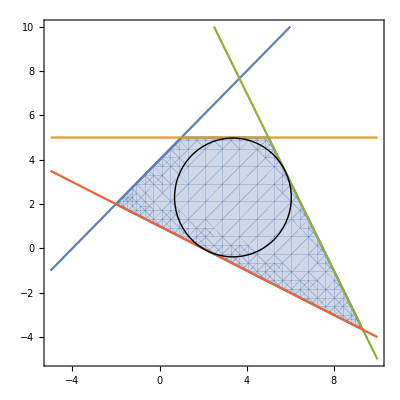

```mathematica
Show[
RegionPlot[-x+y≤4&&y≤5&&2x+y≤15&&x/2+y≥1,{x,-5,10},{y,-5,10}],
ContourPlot[{-x+y==4,y==5,2x+y==15,x/2+y==1},{x,-5,10},{y,-5,10}],
Graphics[Circle[{x,y},r]/.res[[2]]]
]
```

## Naftna rafinerija

Rafinerija iz nafte tipov 1 in 2 meša bencin in kurilno olje. Na voljo ima 5000 sodčkov nafte tipa 1 s kvaliteto 10 in 10000 sodčkov nafte tipa 2 s kvaliteto 5. Povprečna kvaliteta bencina mora biti vsaj 8, povprečna kvaliteta kurilnega olja pa vsaj 6. Za vsak dolar reklame za kurilno olje proda 10 sodčkov kurilnega olja po ceni 20 dolarjev za sodček, za vsak dolar reklame za bencin pa 5 sodčkov bencina po ceni 25 dolarjev za sodček. Kako naj nameša nafto, da bo iztržila čimveč dobička?

### Rešitev

```mathematica
Maximize[{(25-1/5)(b1+b2)+(20-1/10)(k1+k2),b1+k1≤5000,b2+k2≤10000,(10b1+5b2)/(b1+b2)≥8,(10k1+5k2)/(k1+k2)≥6,k1≥0,k2≥0,b1≥0,b2≥0},{k1,k2,b1,b2}]//Timing
```

{2.95313,{323000,{k1→2000,k2→8000,b1→3000,b2→2000}}}

Če neenakosti z enostavnim množenjem spremenimo v linearne, je rešitev znatno hitrejša.

```mathematica
Maximize[{(25-1/5)(b1+b2)+(20-1/10)(k1+k2),b1+k1≤5000,b2+k2≤10000,10b1+5b2≥8(b1+b2),10k1+5k2≥6(k1+k2),k1≥0,k2≥0,b1≥0,b2≥0},{k1,k2,b1,b2}]//Timing
```

{0.,{323000,{k1→2000,k2→8000,b1→3000,b2→2000}}}

## Mešanje tonikov

Na voljo imamo zdravilne tonike A, B in C z vsebnostjo zdravilnh učinkovin I, II in III, podano v spodnji tabeli. Z mešanjem tonikov želimo dobiti napitek, ki bo imel vsebnosti učinkovin, kot so navedene v zadnji vrstici tabele. Natančnih vrednosti ni moč doseči, zato za mero kvalitete mešanice vzamemo po absolutni vrednosti največje odstopanje posamezne učinkovine od predpisane vrednosti (v mešanici, ki vsebuje enak delež vsakega tonika, je ta vrednost enaka 2/3). Kakšni so deleži v najboljši mešanici?

tonik | I | II | III
A | 10 | 2 | 5
B | 15 | 4 | 2
C | 20 | 3 | 3
iskani | 15 | 3 | 4

### Rešitev

```mathematica
Minimize[{Max[Abs[10a+15b+20c-15],Abs[2a+4b+3c-3],Abs[5a+2b+3c-4]],a+b+c==1},{a,b,c}]
```

{5/18,{a→4/9,b→1/6,c→7/18}}